```mathematica
nf1=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ng1=Simplify[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
nf2=Simplify[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ng2=Simplify[g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
nf3=Simplify[f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0}];
ng3=Simplify[g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0}];
```

```mathematica
nf12=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
ng12=Simplify[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
nf32=Simplify[f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0}];
ng32=Simplify[g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0}];
```

```mathematica
NIntegrate[nf1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.44861684 ⅈ

```mathematica
NIntegrate[nf1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.881281759 ⅈ

```mathematica
NIntegrate[nf12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.745699335 ⅈ

```mathematica
NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.44861684 ⅈ

```mathematica
Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,Q->1}]/.{k3->1,y->0.5,θ->π}
```

0.-0.0000163688 ⅈ

```mathematica
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf3t=Together[nf3];
nf3s=Cancel[Simplify[(Numerator[nf3t]-Coefficient[Numerator[nf3t],k1,0])]/Denominator[nf3t]]/.{k1->0};
```

```mathematica
Denominator[nf3t]
```

(-0.9+k1)^2 k1 (1.+k3^2-0.980928 x)^4

```mathematica
NIntegrate[nf3s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.653261002 ⅈ

```mathematica
NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.20464416 ⅈ

```mathematica
nf12=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
nf22=Simplify[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf3t2=Together[nf32];
nf3s2=Cancel[Simplify[(Numerator[nf3t2]-Coefficient[Numerator[nf3t2],k1,0])]/Denominator[nf3t2]]/.{k1->0};
```

```mathematica
NIntegrate[nf12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.06907223 ⅈ

```mathematica
NIntegrate[nf22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.06907223 ⅈ

```mathematica
a2=Import["G:\\calc-online\\gpd\\k-result\\diagram-s-n-he.wdx"];
sf1=Query[1,1]@a2;
sg1=Query[1,2]@a2;
sf2=Query[2,1]@a2;
sg2=Query[2,2]@a2;
sf3=Query[3,1]@a2;
sg3=Query[3,2]@a2;
sf12=sf1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
sf22=sf2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
sf32=sf3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
sg12=sg1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
sg22=sg2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
sg32=sg3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
```

```mathematica
Query[4]@a2
```

第三个是δ，前两个都是0,1-ξ,第一个是不分离的第二个是分离之后的两个应该相等

```mathematica
snf12=Simplify[sf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1}];
snf32=sf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1,k1->0};
snf1=Simplify[sf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
snf3=sf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,k1->0};
```

```mathematica
sng12=Simplify[sg12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1}];
sng32=sg32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1,k1->0};
sng1=Simplify[sg12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
sng3=sg32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,k1->0};
```

```mathematica
NIntegrate[snf1,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf3,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.61136932 ⅈ

```mathematica
NIntegrate[snf1,{y,0,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.15244399 ⅈ

```mathematica
NIntegrate[snf12,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.28802646 ⅈ

```mathematica
NIntegrate[nf1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf1,{y,0,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.03372574 ⅈ

```mathematica
NIntegrate[nf12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf12,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.0337258 ⅈ

```mathematica
NIntegrate[ng12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng12,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-2.71163786 ⅈ

```mathematica
NIntegrate[ng1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng1,{y,0,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-2.71163727 ⅈ

```mathematica
NIntegrate[nf1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.881281759 ⅈ

```mathematica
NIntegrate[nf12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.745699335 ⅈ

```mathematica
NIntegrate[snf1,{y,0,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.15244399 ⅈ

```mathematica
NIntegrate[snf12,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[snf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.28802646 ⅈ

```mathematica
NIntegrate[ng1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.22023678 ⅈ

```mathematica
NIntegrate[sng1,{y,0,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.49140049 ⅈ

```mathematica
NIntegrate[ng12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.08465517 ⅈ

```mathematica
NIntegrate[sng12,{y,0,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[sng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.62698269 ⅈ

```mathematica
(0.012572808460511661 (12.43891074945602+7.053767999999958 Q2+1. Q2^2) cc["C"]^2)/((1.+Q2)^2 (3.5268839999999995+Q2)^2)/.{Q2->1, cc["C"]->2*0.76}
```

0.00726205

```mathematica
2.0337257955631496476`9.392911205626886*(2*0.76)^2/(0.093^2*6*(2π)^4*2)
```

0.0290478

```mathematica
0.029047780656956002/4
```

0.00726195

```mathematica
-(0.01676374461401548 (12.438910749456294 Q2+7.053768000000033 Q2^2+1. Q2^3) cc["C"]^2)/(Q2 (1.+Q2)^2 (3.5268839999999995+Q2)^2)/.{Q2->1, cc["C"]->2*0.76}
```

-0.00968274

```mathematica
-2.7116372723187803991`9.605465449343445 *(2*0.76)^2/(0.093^2*6*(2π)^4*2)
```

-0.0387304

```mathematica
-0.038730415319205506/4
```

-0.0096826

```mathematica
snf1[y_]=Simplify[sf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
snf3=sf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,k1->0};
sng1[y_]=Simplify[sg12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
sng3=sg32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,k1->0};
nf1[y_]=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ng1[y_]=Simplify[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
nf3=Simplify[f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0}];
ng3=Simplify[g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0}];
```

```mathematica
rinf[y_]:=NIntegrate[nf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ring[y_]:=NIntegrate[ng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
sinf[y_]:=NIntegrate[snf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
sing[y_]:=NIntegrate[sng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
rlf=ParallelTable[{y,rinf[y]},{y,0,0.9,0.01}];
rlg=ParallelTable[{y,ring[y]},{y,0,0.9,0.01}];
slf=ParallelTable[{y,sinf[y]},{y,0,1.1,0.01}];
slg=ParallelTable[{y,sing[y]},{y,0,1.1,0.01}];
```

```mathematica
rf=Interpolation[rlf];
rg=Interpolation[rlg];
sf=Interpolation[slf];
sg=Interpolation[slg];
```

```mathematica
pathrf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"r-f-0.1.pdf"}];
Export[pathrf01,Labeled[Show[Plot[(-I)*rf[x],{x,0,0.9},PlotRange->{{0,0.9},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,r],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\r-f-0.1.pdf

```mathematica
pathrg01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"r-g-0.1.pdf"}];
Export[pathrg01,Labeled[Show[Plot[(-I)*rg[x],{x,0,0.9},PlotRange->{{0,0.9},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,r],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\r-g-0.1.pdf

```mathematica
pathsf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"s-f-0.1.pdf"}];
Export[pathsf01,Labeled[Show[Plot[(-I)*sf[x],{x,0,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,s],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\s-f-0.1.pdf

```mathematica
pathsg01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"s-g-0.1.pdf"}];
Export[pathsg01,Labeled[Show[Plot[(-I)*sg[x],{x,0,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,s],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\s-g-0.1.pdf

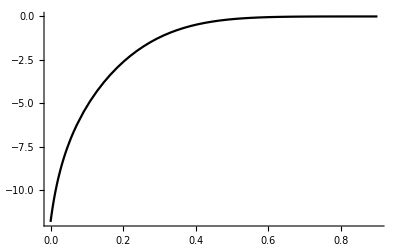
-Graphics-f_ryξ=0.1

```mathematica
Labeled[Show[Plot[(-I)*rf[x],{x,0,0.9},PlotRange->{{0,0.9},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,r],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```